A Minimal Model for Biodiversity

Willem Nielsen

So in his article Wolfram mainly focuses on the programs go from short to long and therefore, from simple to complex. In an attempt to model bacterial resistance, I examined another dimension, that of diversity. One approach is to start with a rule and then explicitly look for “new ideas”. That is, look for automata with the pattern that is most different from any of its predecessors, judged by difference in corresponding boxes.

So we start with this rule here.

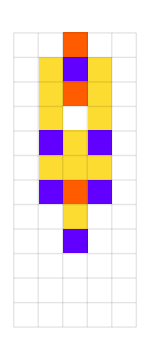

```mathematica
plotfit[#, ImageSize->150]&@trirule
```

Then we generate a bunch of random mutations and select only ones that are about the same length. Of those, we select the one that is most different from the previous automata. In this case, this was the most different. There is a few yellow boxes on the bottom left that are added.

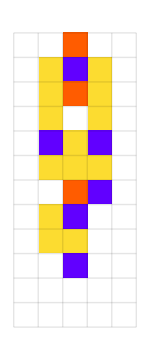

```mathematica
plotfit[ getmostdiff[{trirule}][[-1]], ImageSize->150]
```

We do this recursively and basically ask the question, how different can we get? And somewhat remarkably, this simple procedure is able to continuously find new automata of similar length.

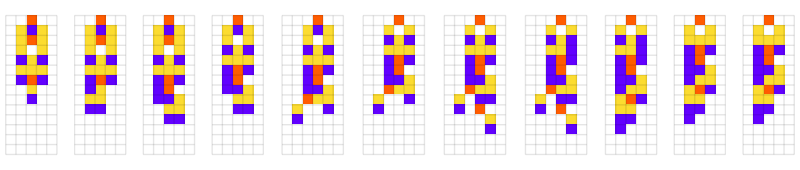

```mathematica
GraphicsRow[plotfit/@diffsmemo[[3]], ImageSize->{800, Automatic}]
```

The way in which this happens varies greatly. In this cases we basically had one radical idea.

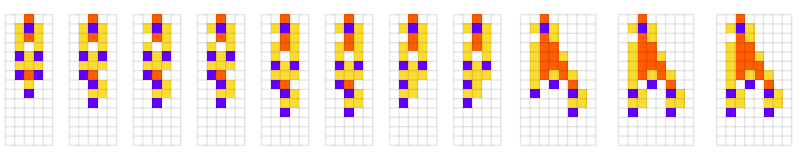

```mathematica
GraphicsRow[plotfit/@diffsmemo[[6]], ImageSize->{800, Automatic}]
```

In this case we get stuck.

```mathematica
AppendTo[diffsmemo, Nest[getmostdiff, {trirule}, 10]];
```

TakeLargestBy::insuff: Cannot take 1 element(s) from a list of length 0.

CellularAutomaton::rlist: The neighborhood specification cannot be computed from the list of rules {}.

CellularAutomaton::nspecnl: Rule specification [◼] | RandomRuleMutation [{}] should be an Integer, a List, a pure Boolean function, a String, or an Association.

CellularAutomaton::kspec: Since position 1 of rule specification {100,All} is not a function or rule list, position 2 (if present) must be of the form k, {k, 1}, or {k, wts} where k is a machine integer > 1 and wts is a non-empty array of non-negative machine integers.

CellularAutomaton::nspecnl: Rule specification [◼] | RandomRuleMutation [{}] should be an Integer, a List, a pure Boolean function, a String, or an Association.

CellularAutomaton::kspec: Since position 1 of rule specification {100,All} is not a function or rule list, position 2 (if present) must be of the form k, {k, 1}, or {k, wts} where k is a machine integer > 1 and wts is a non-empty array of non-negative machine integers.

CellularAutomaton::nspecnl: Rule specification [◼] | RandomRuleMutation [{}] should be an Integer, a List, a pure Boolean function, a String, or an Association.

General::stop: Further output of CellularAutomaton::nspecnl will be suppressed during this calculation.

CellularAutomaton::kspec: Since position 1 of rule specification {100,All} is not a function or rule list, position 2 (if present) must be of the form k, {k, 1}, or {k, wts} where k is a machine integer > 1 and wts is a non-empty array of non-negative machine integers.

General::stop: Further output of CellularAutomaton::kspec will be suppressed during this calculation.

TakeLargestBy::insuff: Cannot take 1 element(s) from a list of length 0.

CellularAutomaton::rlist: The neighborhood specification cannot be computed from the list of rules {}.

TakeLargestBy::insuff: Cannot take 1 element(s) from a list of length 0.

General::stop: Further output of TakeLargestBy::insuff will be suppressed during this calculation.

CellularAutomaton::rlist: The neighborhood specification cannot be computed from the list of rules {}.

General::stop: Further output of CellularAutomaton::rlist will be suppressed during this calculation.

```mathematica
GraphicsRow[plotfit[#, ImageSize->60]&/@DeleteCases[diffsmemo[[5]], {}]]
```

-Graphics-

In this case, we have an explosion of new ideas.

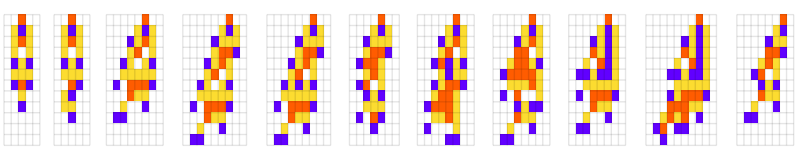

```mathematica
GraphicsRow[plotfit[#]&/@diffsmemo[[10]], ImageSize->{800, Automatic}]
```

And we can see that each time we go in a different direction. This shows us that the space of automata is very rich. So how far can this process go? Here is a run after 30 steps:

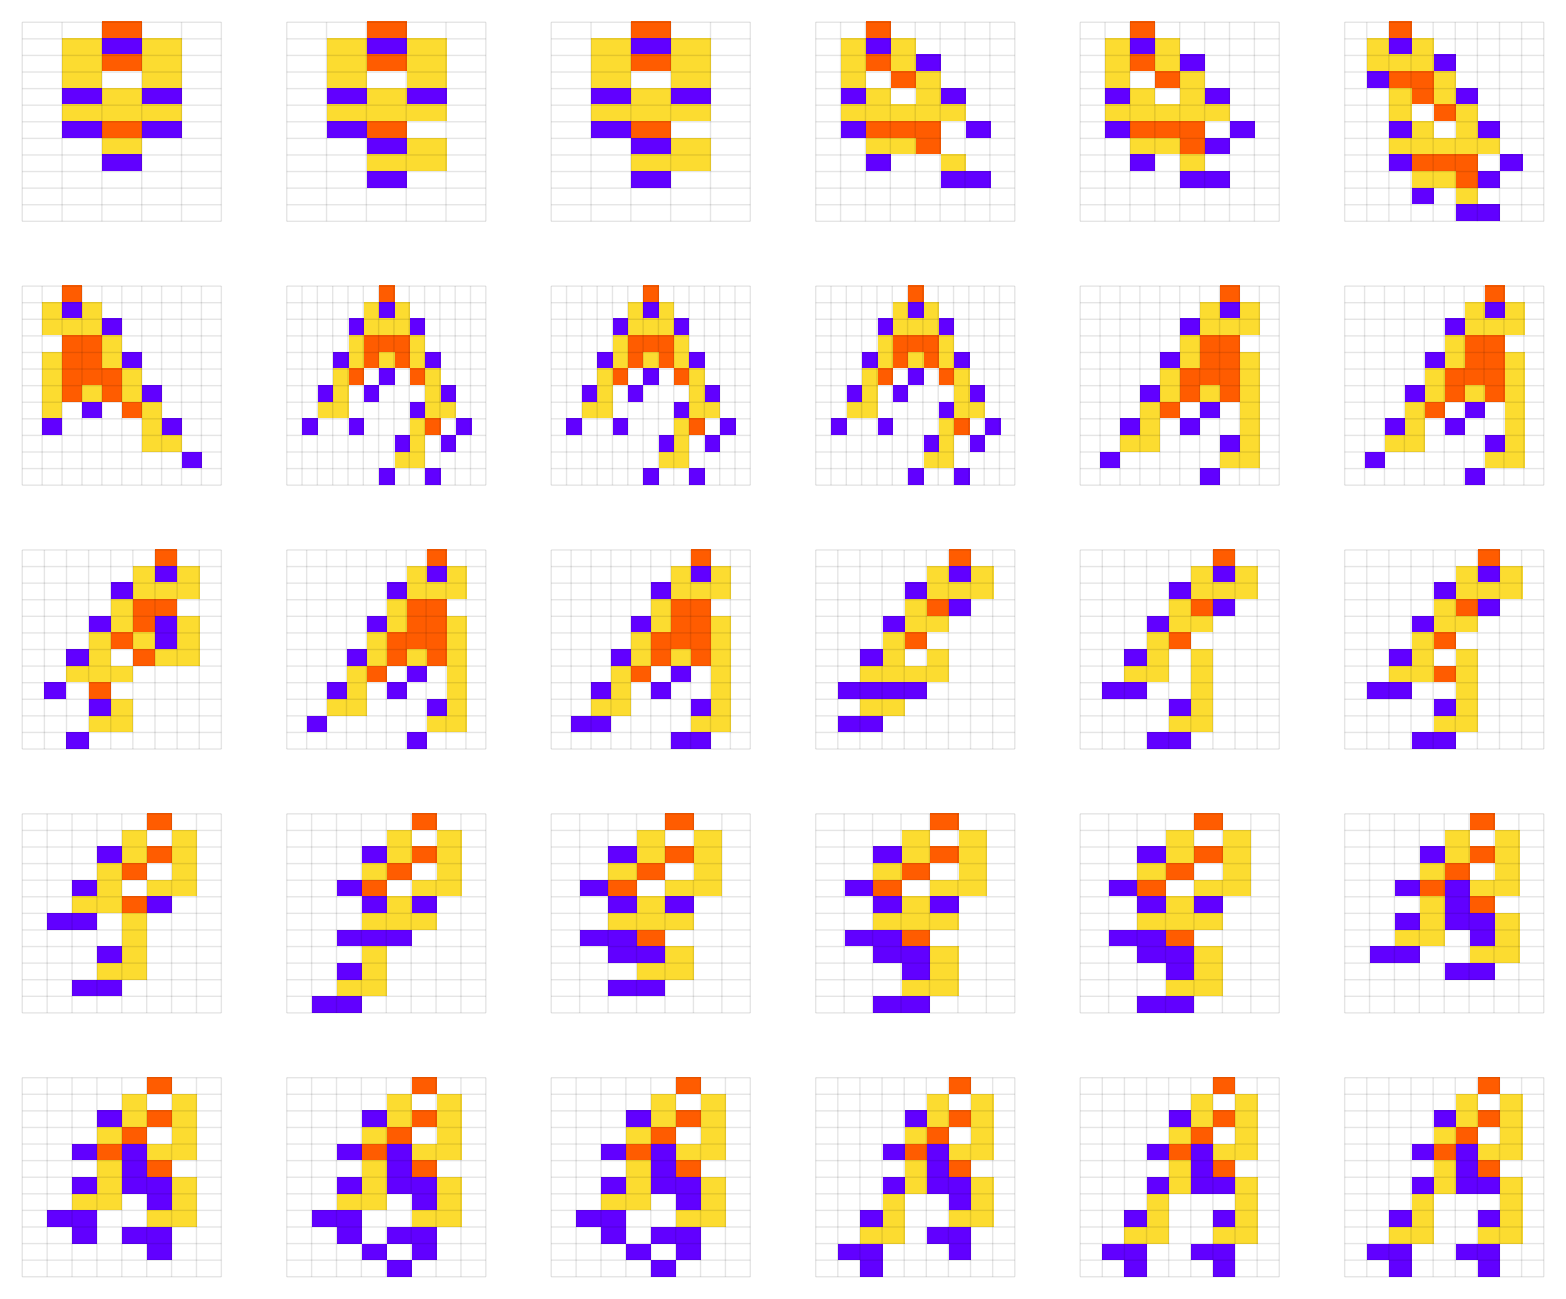

```mathematica
GraphicsGrid[Partition[plotfit[#]&/@diffsmemo[[13]], 6]]
```

Notice how there are new ideas continuously discovered

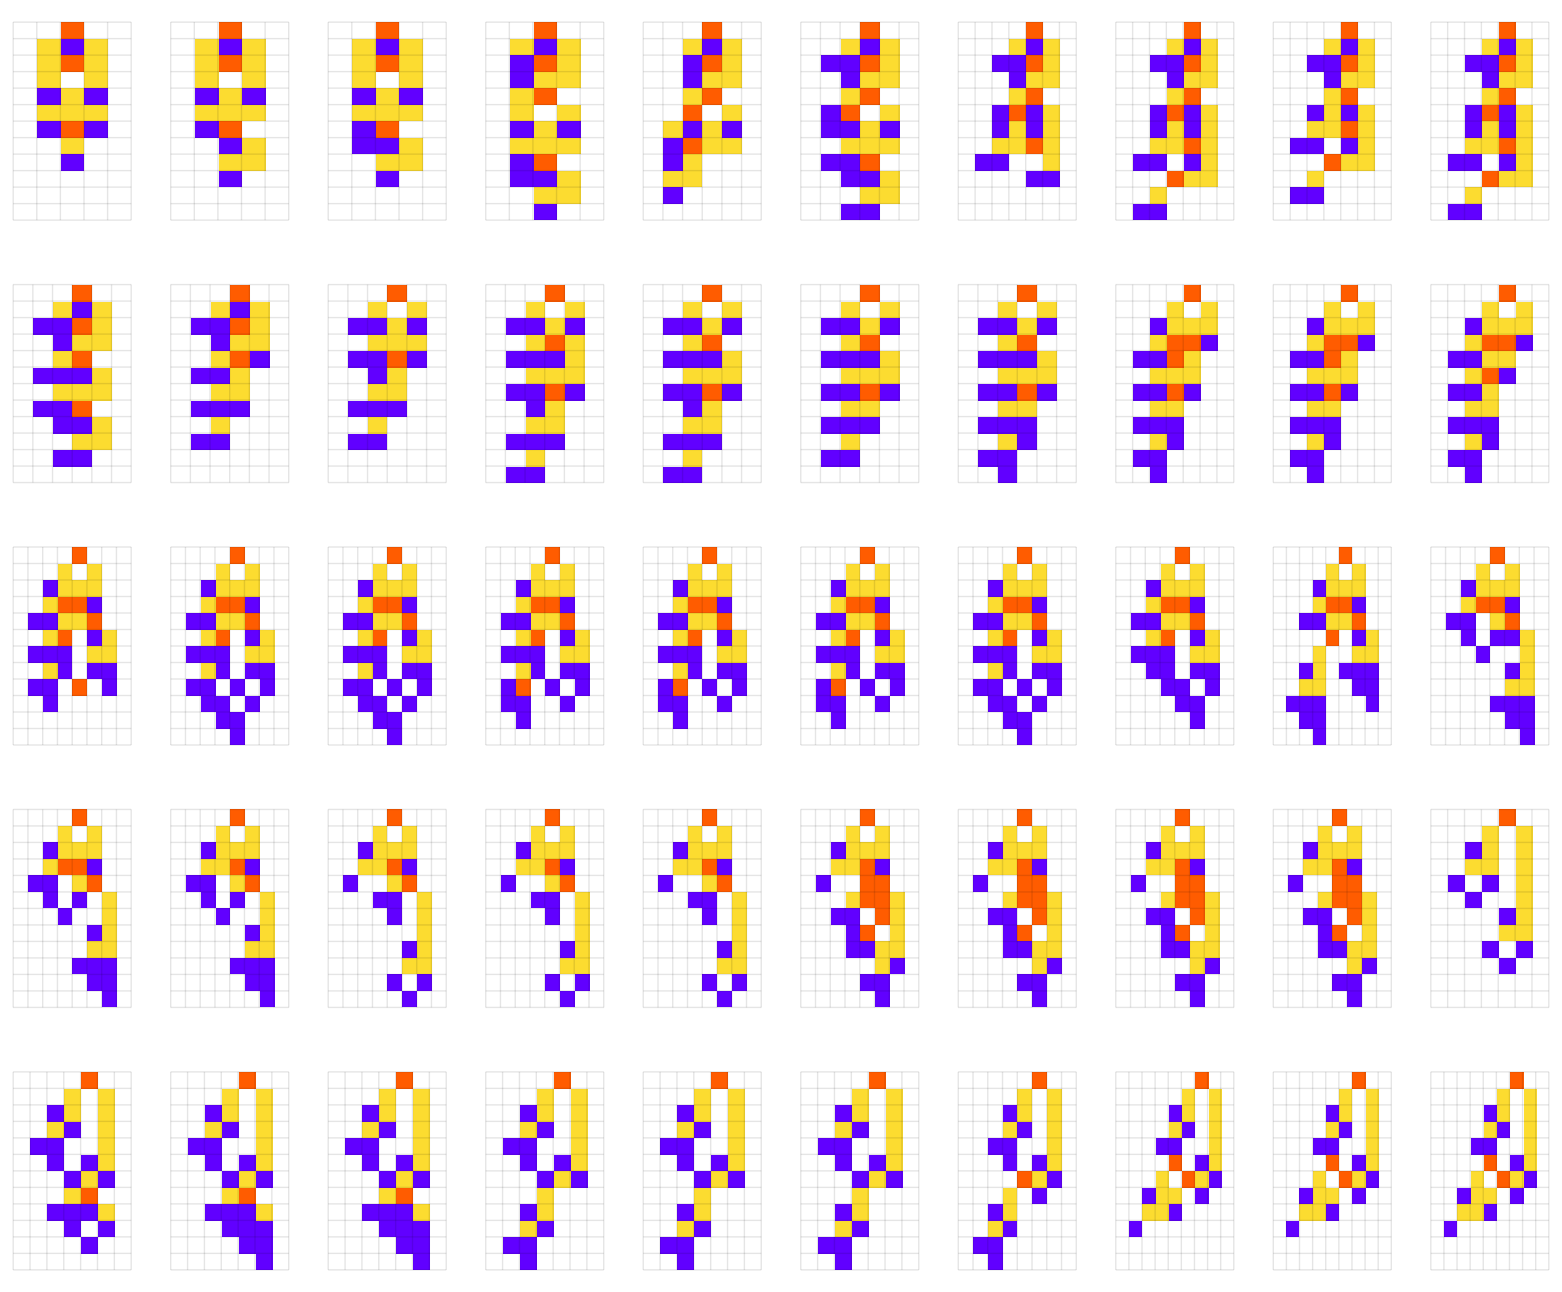

```mathematica
GraphicsGrid[Partition[plotfit/@diffsmemo[[14]], 10]]
```

We can see that process continues to be able to find new solutions. To quantify how the automata change over time, we can look at the number of boxes that are different from the initial automata.

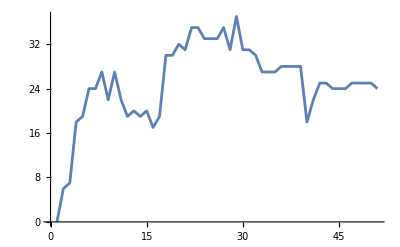

```mathematica
ListLinePlot[getdiffrule[trirule, #]& /@ diffsmemo[[-1]]]
```

One take away here, is the “pace of innovation” seems to jump around a lot. Also, there is a rapid increase at the start followed by a plateauing effect. This is because the automata can only become so different from the initial. But, if we instead use a feature space plot we can get a better sense of  the rate of innovation. Here is that same run with the line darkening over time.

```mathematica
plots = plotfit[#, ImageSize->30]&/@ diffsmemo[[14]];
callouts = MapThread[Callout[#1,Style[#2], Automatic,LeaderSize->15,LabelVisibility->All,Background->None]&, {coords14,plots }];
ListLinePlot[callouts, Mesh->All,MeshStyle->PointSize[0.01],PlotStyle->Directive[Thick,LightGray], PerformanceGoal->"Quality", ColorFunction->Function[{x,y},Blend[{Black, LightGray},x]], Frame->False, Axes->False]
```

-Graphics-

And if we look at the speed of innovation in feature space over time we don’t see the slowdown from before. Here we just take the distances of each step in the plot above.

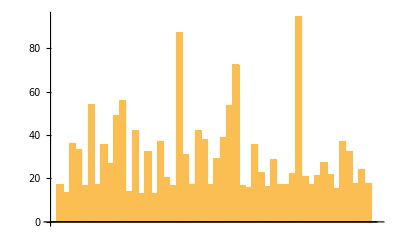

```mathematica
coordpairs = Partition[coords14, 2, 1];
dists = EuclideanDistance@@@coordpairs;
BarChart[dists]
```

And the thing to observe here is while there are large fluctuations, the overall rate of innovation stays pretty much constant, which we will see later is not always the case. So we’ve been looking at k = 4, r = 1 automata, does this work with k = 3?

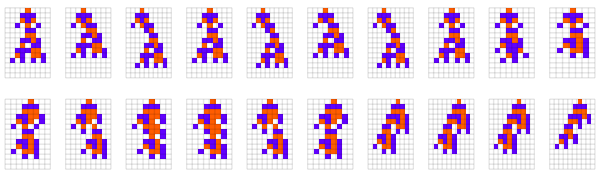

```mathematica
GraphicsGrid[Partition[plotfit/@diffsmemo[[47]], 10], ImageSize->{600, Automatic}]
```

So we can see that it still works, let’s go further with a run of 50 steps.

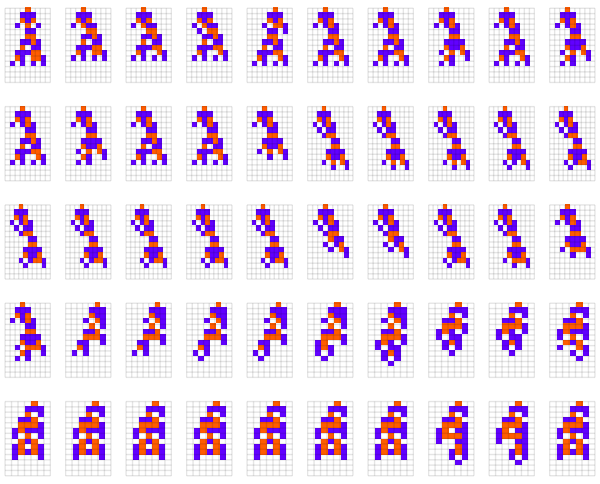

```mathematica
GraphicsGrid[Partition[plotfit/@diffsmemo[[48]], 10], ImageSize->{600, Automatic}]
```

If you look carefully you can see that the 2-color automata tend to get stuck on one idea for longer. This is because there is simply less solutions. Interestingly, when it does make a jump though, the jump is usually huge. This can be seen in the graph of the differences of each automata with the initial automata.

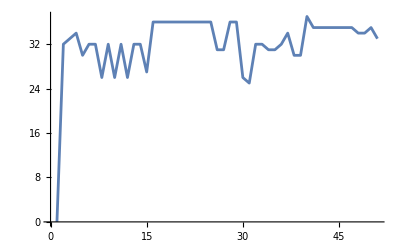

```mathematica
ListLinePlot[getdiffrule[initrule, #]& /@ diffsmemo[[48]]]
```

Notice  how  it  has  a  big  jump  to  30, and  then  has a stretch where it is alternating between two of the same idea:

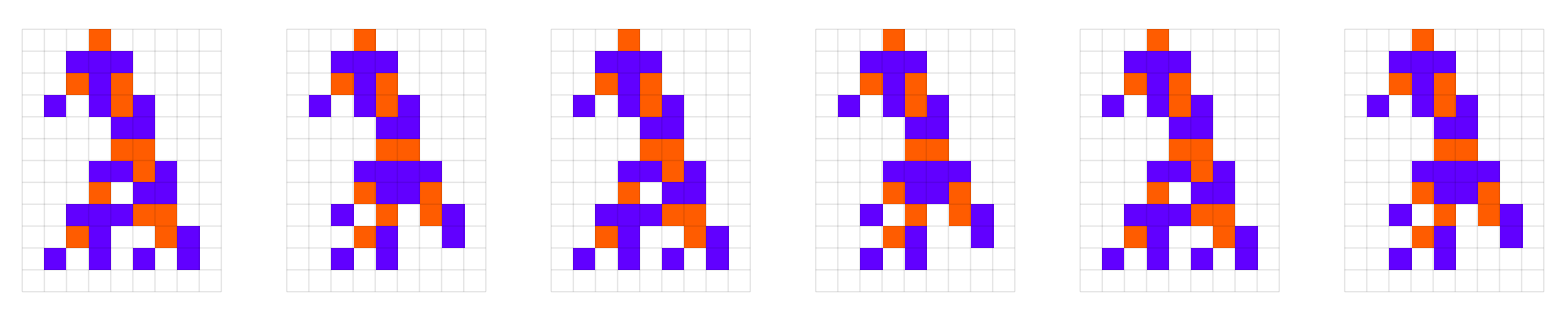

```mathematica
GraphicsRow[plotfit[#]&/@ diffsmemo[[48, 7;;12]]]
```

We never saw something like this with the three color. Now, it’s an interesting question: “How  does evolution vary with each generation?”. Does biological evolution prefer many small changes or a few large ones? I think this an interesting question to pursue; Empirically, it seems that it prefers very small changes and non-random ones. Like the shape of human bodies for example. There is clearly some purposeful distribution of height, weight and dimensions, but you very rarely see someone randomly grow a third leg. Evolution is conservative in this way. I think there is something very deep here related to risk-taking principles that all surviving systems must follow, and I’m going to explore that extensively in a different article.

But okay, let’s look at the feature space plot of the 2-color automata to get a better sense of what’s going on.

```mathematica
plotsk3=(plotfit[#1,ImageSize->22]&)/@diffsmemo⟦48⟧;
callouts = MapThread[Callout[#1,Style[#2], Automatic,LeaderSize->15,LabelVisibility->All,Background->None]&, {coords48, plotsk3 }];
ListLinePlot[callouts, Mesh->All,MeshStyle->PointSize[0.01],PlotStyle->Directive[Thick,LightGray], PerformanceGoal->"Quality", ColorFunction->Function[{x,y},Blend[{LightGray, Black},x]], Frame->False, Axes->False]
```

-Graphics-

Again, we can see that change is less continuous, with a bunch of bouncing around in one place followed by a large jump into a new area. Looking at the “derivative of diversity” below we see a similar theme, with much larger jumps than before:

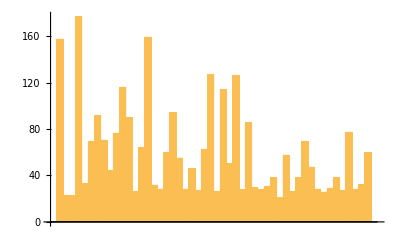

```mathematica
coordpairs = Partition[coords48, 2, 1];
dists = EuclideanDistance@@@coordpairs;
BarChart[dists]
```

We can also note that while the rate fluctuates greatly between individual steps, the overall rate seems to be staying convex, something we’ll see does not hold when we add multiple organisms.

So we’ve been looking pretty much at how one single automata can change over time, by selecting the automata that are most different from it. And the takeaway has been that the process makes large jumps but overall moves further and further out into feature space at a constant rate. But in the real biological world, there are many cases where descendants evolve separately, for whatever reason. How would that change the process of diversification? To answer this we can do the multiway equivalent of the above process. The k = 4 case is a bit harder to deal with so we’ll look at the k = 3.

After searching the mutation graph 8 steps deep, we come up with this multiway graph of possible new automata.

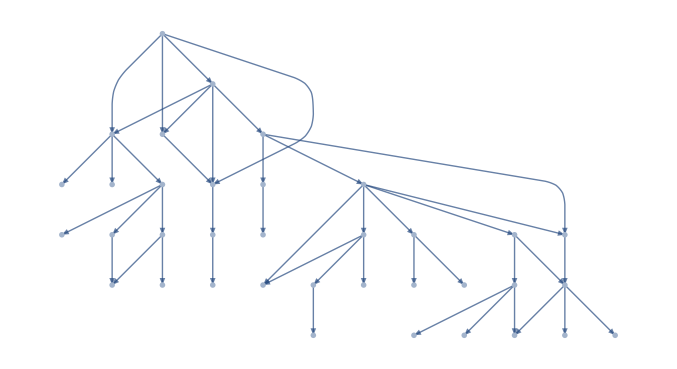

```mathematica
ef = DeleteDuplicatesBy[pgmemo[[8]], Sort];
Graph[ef,VertexShapeFunction->(Inset[plotca[#2, ImageSize->{30, 40}], #1]&) , GraphLayout->"LayeredDigraphEmbedding", EdgeShapeFunction->{{ "Arrow", "ArrowSize"->0.025}}]
```

But at steps 9 and 10, something amazing happens, here’s the graph after 10 steps:

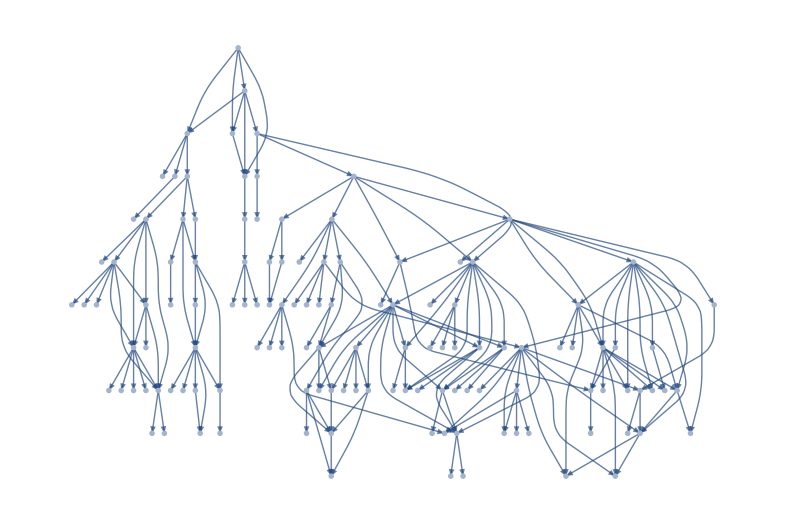

```mathematica
ef = DeleteDuplicatesBy[pgmemo[[10]], Sort];
Graph[ef,VertexShapeFunction->(Inset[plotca[#2, ImageSize->{18, 30}], #1]&) , GraphLayout->"LayeredDigraphEmbedding", EdgeShapeFunction->{{ "Arrow", "ArrowSize"->0.01}}, AspectRatio->2/3]
```

We get an explosion of new discoveries at step 9 and 10. Here’s the graph in a different embedding.

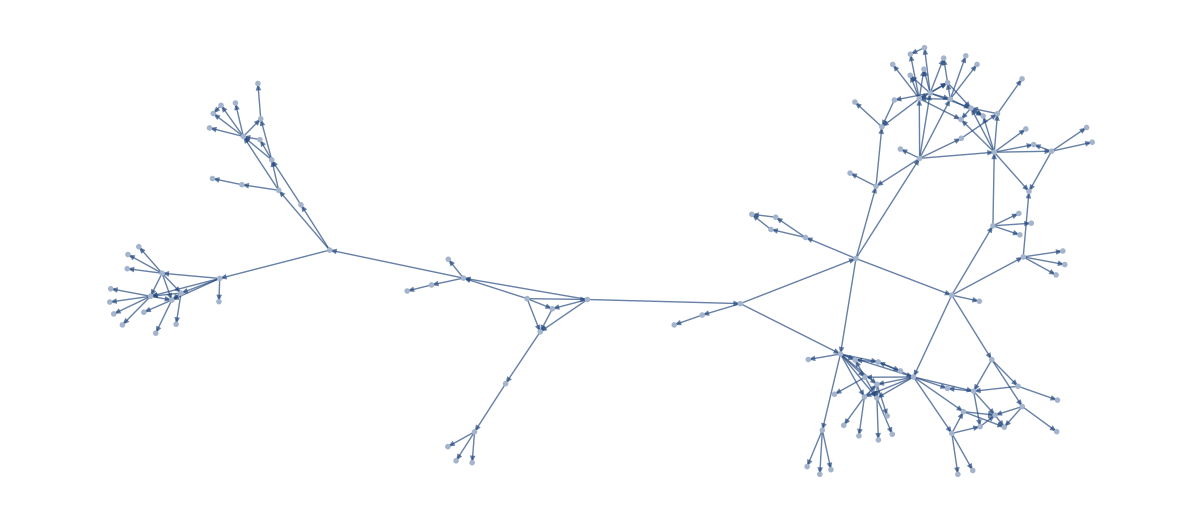

```mathematica
ef = DeleteDuplicatesBy[pgmemo[[10]], Sort];
Graph[ef,VertexShapeFunction->(Inset[plotca[#2, ImageSize->{18, 30}], #1]&) , EdgeShapeFunction->{{ "Arrow", "ArrowSize"->0.01}}]
```

To give you a sense of the dramatic shift at steps 9 and 10, here are the new discoveries of the first 6 steps:

```mathematica
Column[Row/@clean[[;;6]]]
```

-Graphics--Graphics-
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics-

Pretty underwhelming. And here are the new discoveries for the last 4 steps:

```mathematica
GraphicsRow[ggs[[7;;]]]
```

-Graphics-

This happens because we’re searching a high dimensional space. So with each step we increase the number of nodes searched exponentially. Here is the number of nodes searched as we go deeper into the search tree.

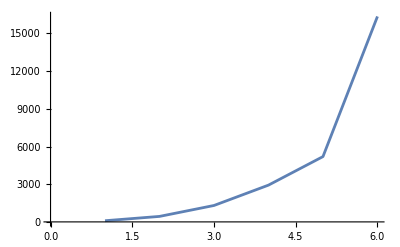

```mathematica
ListLinePlot[Length/@ mgmemo]
```

And here’s the graph of new automaton discovered:

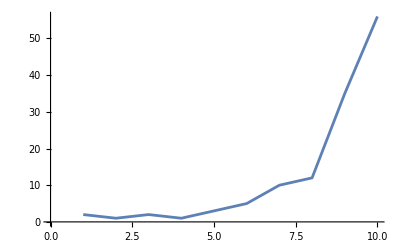

```mathematica
ListLinePlot[Length/@ clean]
```

One question here is, “Are we just getting more ‘species’ or are we actually getting more diversity”.  In other words, are we moving inwards, getting a more and more detailed graph? Or are we actually expanding out into phenotype space? And if you look at the progressive phenotype graphs below, it’s not clear whether we’re actually expanding our graph in phenotype space.

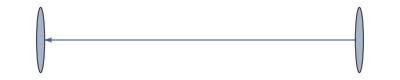
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Graph[#]&/@ pgmemo
```

To answer this we can graph all our automata in feature space, and progressively add the automata at each step. If the automata appear to spread out, then we know they’re actually breaking new ground.

```mathematica
fspmulti
```

-Graphics-

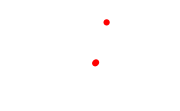
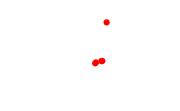
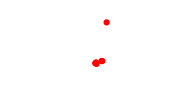
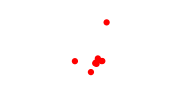
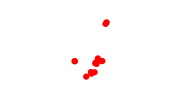
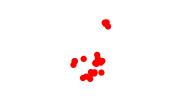
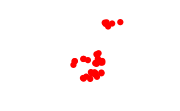
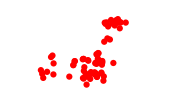
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
acc = Accumulate[Length/@ clean];
ListPlot[coordsmulti[[;;#]],PlotRange->{{-15, 15},{-15, 15}}, ImageSize->Small, PlotStyle->{PointSize[0.025],Red}, Axes->False, PlotHighlighting->None]&/@ acc
```

So it appears that it is expanding into feature space, although not at every step. For instance, the jump between 8 and 9 gives a huge expansion, but between 9 and 10 we mostly move inward.

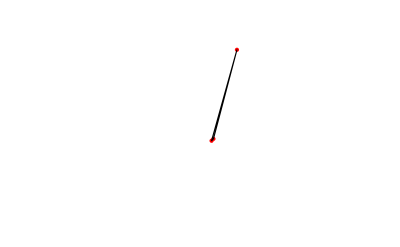
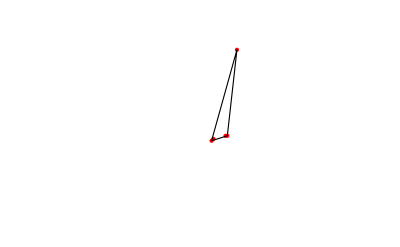
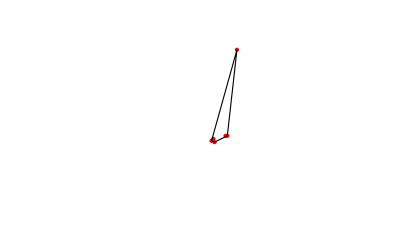
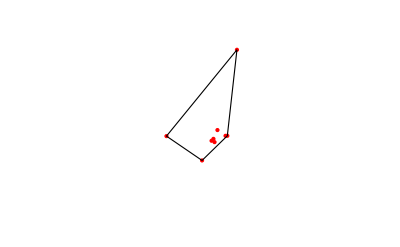
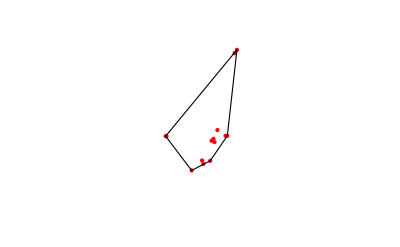
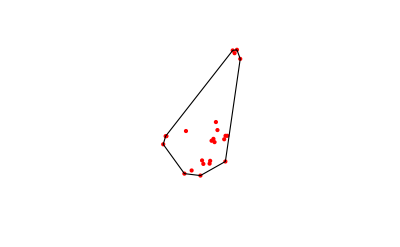
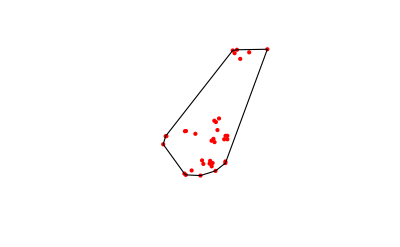
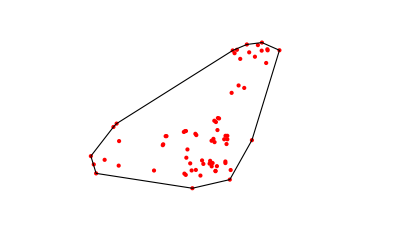

```mathematica
hulls=ConvexHullMesh[coordsmulti[[;;#]]]&/@ acc[[2;;]];
MapThread[Show[ListPlot[coordsmulti[[;;#1]],PlotStyle->{Red,PointSize[Small]}, PlotRange->{{-15, 15},{-15, 15}}, Axes->False],Graphics[{EdgeForm[Black],FaceForm[None],#2}]]&, {acc[[2;;]], hulls}]
```

Here we plot the area of each region.

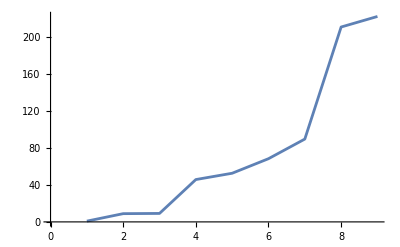

```mathematica
ListLinePlot[RegionMeasure/@ hulls]
```

We’re definitely increasing, and it’s definitely convex up to step 9, but we may be hitting a wall at step 10.

So why does this work? Why is it that it is always possible to find a new type of automata? And why do we see this rapid change in the rate of discovery? Is this consistent with biology here on earth? To answer these questions, it’s helpful to look at a simpler model. We’ll ignore the organism and just focus on the genes. Here we show a very small mutation graph with a genome that is 5-bits:

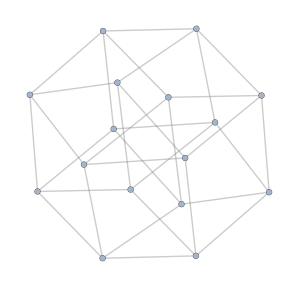

```mathematica
ug = UndirectedGraph[Catenate[Table[#->MapAt[1-#&,#,i],{i,Length[#]}]&/@Tuples[{1,0},4]],EdgeStyle->Opacity[.4,Gray]];
ug2 = Graph[ug, VertexLabels->{x_:>Placed[ArrayPlot[{Append[x,0]},
Mesh->True,ImageSize->40],Center]}]
```

Now instead of looking for automata of a constant length, we will just randomly define a set of genes to be “fit”. Here we randomly choose 3 genes to be fit:

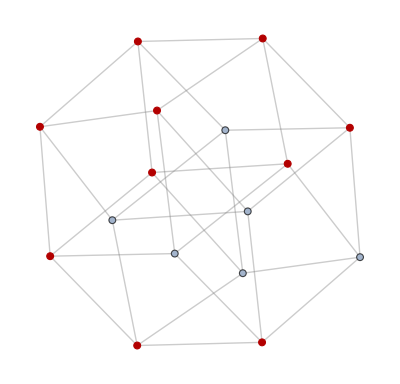

```mathematica
HighlightGraph[ug, rand = RandomSample[VertexList@ug, 10]]
```

So how can evolution move through the “fitness space”? Here’s the subgraph containing only the fit genotypes:

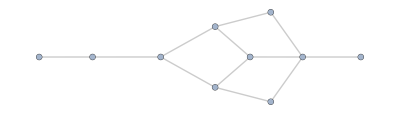

```mathematica
Subgraph[ug2, rand]
```

Pretty underwhelming. And nothing like we saw with our automata explosion. Things start to get interesting though when you increase the size of genome. Here’s a 7-bit genome space:

```mathematica
ug6 = Graph[ugs[[6]], VertexLabels->{x_:>Placed[ArrayPlot[{Append[x,0]},
Mesh->True,ImageSize->40],Center]}]
```

-Graphics-

Taking a random fitness sample we get:

```mathematica
HighlightGraph[ugs[[6]], rand = RandomSample[VertexList@ugs[[6]], 30], VertexSize->0.2]
```

-Graphics-

And here is the fitness space:

```mathematica
Subgraph[ugs[[6]], rand, VertexLabels->{x_:>Placed[ArrayPlot[{Append[x,0]},
Mesh->True,ImageSize->40],Center]}]
```

-Graphics-

Now we’re starting to get to a level of dimensionality that could produce an explosion of new ideas like we saw above. Let’s keep increasing the size of the genome space, here with a 10-bit genome:

```mathematica
HighlightGraph[ugs[[9]], rand = RandomSample[VertexList@ugs[[9]], 250], VertexSize->0.6]
```

-Graphics-

And the fitness space:

```mathematica
sg = Subgraph[ugs[[9]], rand]
```

-Graphics-

Looking at the search graph of fitness space starting from a random source:

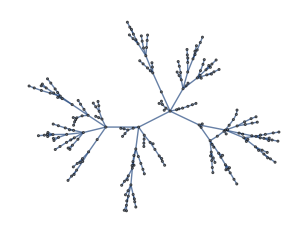

```mathematica
bfs = Reap[BreadthFirstScan[sg, 
  RandomChoice[rand],{"FrontierEdge"->Sow}]][[2, 1]];
bfsg = Graph[bfs]
```

With this graph you can clearly see the outward explosions in diversity that we saw initially. So we’re seeing that even in a 10-bit genome, if you have multiple organisms and search in multiple directions at once, then explosions are inevitable. One thing I didn’t mention, is how large I’m making the fitness set. And indeed, even with a 10 bit genome, if the fitness set is small, evolution won’t be able to expand quickly. Here we show what happens if our fitness set is only 100 out of 512 genes:

```mathematica
rand = RandomSample[VertexList@ugs[[9]], 100];
```

```mathematica
sg = Subgraph[ugs[[9]], rand]
```

-Graphics-

Here don’t see nearly the connectivity we saw before, indicating that the speed limit on bio-diversification is quite slow. So we’ve seen two critical factors in the rate of diversification. First, you need to have a genome that is high dimensional. Second, you need enough solutions. To generaliz the point, ,

### Reference

```mathematica
Table[AppendTo[diffsmemo, Nest[getmostdiff, {trirule}, 10]], 10];
```

```mathematica
diffs = Map[getdiffrule[trirule, #]& , Delete[diffsmemo, {{5}, {8}}], {2}];
```

```mathematica
diffs = Map[getdiffrule[trirule, #]& , diffsmemo[[{3, 6, 10}]], {2}];
```

So my idea here, is to examine what Wolfram calls “fitness-neutral” sets. We start with k = 2, r = 3/2 because the multiway graph is manageable.

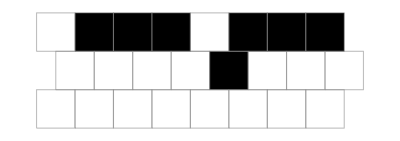
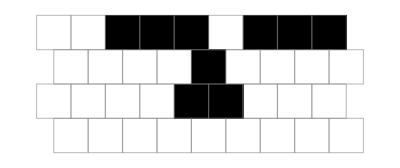
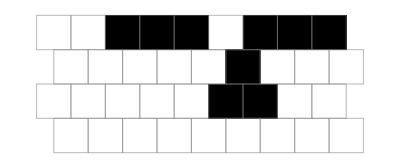
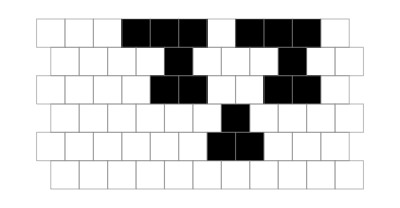
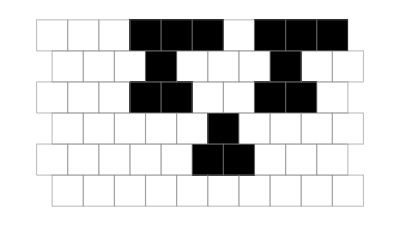
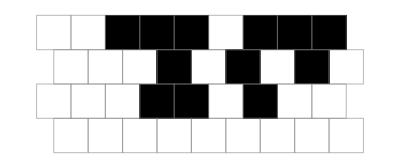
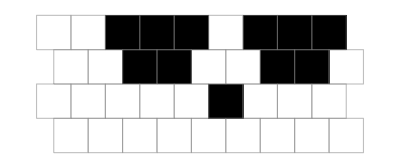
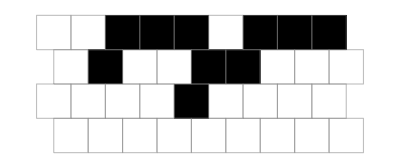

```mathematica
Module[{res,sublevels,vfs},
res=Reap[{{"[◼]", "EvolutionGraph"}}[2,3/2,
GraphLayout->"LayeredDigraphEmbedding"],
"SubLevels"];
sublevels=res[[2,1,1]];
res=res[[1]];
vfs=Association[KeyValueMap[Function[{key,rules},key->
{{"[◼]", "SerratedBricksArrayPlot"}}[#,ImageSize->{Automatic,(2+key[[1]])10}]
&@First[Union[CellularAutomaton[{#,2,3/2},{{1,1,1,0,1,1,1},0},
key[[1]]]&/@rules]]
],sublevels]];
Graph[res,
GraphLayout->"LayeredDigraphEmbedding",AspectRatio->2/3,
EdgeStyle->Gray,
VertexSize->1/2,
VertexShapeFunction->Function[
Inset[vfs[#2],#1,Automatic,
Times[#3[[1]],
#/Last[#]&@ImageDimensions[vfs[#2]],
Sqrt[First[#2]+5]
]
]
],
PerformanceGoal->"Quality"
]
]
```

And here are some examples of various fitness-neutral sets.

```mathematica
Module[{mg,res,sublevels,vfs},
mg={{"[◼]", "MutationGraph"}}[2,3/2];
res=Reap[{{"[◼]", "EvolutionGraph"}}[2,3/2,
GraphLayout->"LayeredDigraphEmbedding"],
"SubLevels"];
sublevels=res[[2,1,1]];
sublevels=Map[Subgraph[mg,#]&,sublevels];
sublevels=Lookup[sublevels,{{3,6},{3,5},{6,7},{7,1}}];
Graph[#,
VertexSize->1/2,PerformanceGoal->"Quality",
EdgeStyle->Gray,ImageSize->{UpTo[350],200},
VertexShapeFunction->Function[
Inset[{{"[◼]", "SerratedBricksArrayPlot"}}[
CellularAutomaton[{#2,2,3/2},
{{1,1,1,0,1,1,1},0},
{{"[◼]", "TestLifetime"}}[{#2,2,3/2},
{1,1,1,0,1,1,1},
10]]
],#1,Automatic,
{Automatic,Last[#3] Sqrt[({{"[◼]", "TestLifetime"}}[
{#2,2,3/2},
{1,1,1,0,1,1,1},10]+1)]}
]]
]&/@sublevels
]
```

```mathematica
{-Graphics-,,,-Graphics-}
```

## Functions and Parameters

```mathematica
testlifetime = {{"[◼]", "TestLifetime"}}; randomrulemutation = {{"[◼]", "RandomRuleMutation"}};
rulesmutationplot = {{"[◼]", "RulesMutationPlot"}}; customstyledata = {{"[◼]", "CustomStyleData"}};
```

```mathematica
k = 3; r = 1; initrule = {5586032021307, 3, 1}; trirule = {109636419052937157723438118980837975564,4,1};
longrule = {5600111605818,3,1};
initconditions = {0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0};
nsteps = 11; initlifetime = testlifetime[initrule];
```

```mathematica
getca[rule_] := CellularAutomaton[rule, initconditions, nsteps]
```

```mathematica
plot[{ruleidx_, k_, r_}, OptionsPattern[{ColorRules->customstyledata["Colors"], ArrayPlot}]] :=  Module[{ca},
  ca = getca[{ruleidx, k, r}];
  ArrayPlot[ca,  ColorRules->OptionValue[ColorRules],
   Mesh -> True, MeshStyle -> Opacity[.1], ImageSize -> OptionValue[ImageSize]
   ]]

Options[plotfit] = {"init"->initconditions, "padding"->1, "nsteps"->nsteps};
plotfit[{ruleidx_, k_, r_}, OptionsPattern[{ColorRules->customstyledata["Colors"], plot, ArrayPlot}]] :=  Module[{ca},
  ca = ArrayPad[#, OptionValue["padding"]]& /@ getca[{ruleidx, k, r}, OptionValue["init"], OptionValue["nsteps"]];
  ArrayPlot[ca,  ColorRules->OptionValue[ColorRules],
   Mesh -> True, MeshStyle -> Opacity[.1], ImageSize -> OptionValue[ImageSize]
   ]]

plot[ruleidx_Integer] := Module[{ca},
  ca = getca[{ruleidx, k, r}];
  ArrayPlot[ca, ColorRules -> customstyledata["Colors"],
   Mesh -> True, MeshStyle -> Opacity[.1], ImageSize -> {165, Automatic}
   ]]
```

```mathematica
getmostdiff[rules_]:= Module[{auto, mutes, selected, autos, diffs},
 auto = getca[rules[[-1]]];
 mutes = Table[randomrulemutation[rules[[-1]]], 100];
 selected = Select[mutes,withinrange[#, 10, 12]&];
 If[selected == {}, Append[rules, rules[[-1]]],
 Append[rules, TakeLargestBy[selected, getdiffs[rules, #]&, 1][[1]]]]
]
```

```mathematica
ClearAll@phenoedges
```

```mathematica
getcaedge[start_->dest_]:= getca[start]->getca[dest]

phenoedges[graph_]:=Module[{},
es = EdgeList@graph;
caedges = getcaedge/@ EdgeList[graph];
DeleteCases[DeleteDuplicates[caedges],x_->x_]
]
```

## Saving and loading

```mathematica
Export["Projects/Wolfram/CAEvolution/diffsmemo/diffsmemo.csv", diffsmemo]
```

Projects/Wolfram/CAEvolution/diffsmemo/diffsmemo.csv

```mathematica
Export["Projects/Wolfram/CAEvolution/diffsmemo/coordsk3.csv", coordsk3]
```

Projects/Wolfram/CAEvolution/diffsmemo/coordsk3.csv

```mathematica
Export["Projects/Wolfram/CAEvolution/graphmemo.csv", graphmemo]
```

Projects/Wolfram/CAEvolution/graphmemo.csv

```mathematica
Export["Projects/Wolfram/CAEvolution/pgmemo.csv", pgmemo]
```

Projects/Wolfram/CAEvolution/pgmemo.csv

```mathematica
Export["Projects/Wolfram/CAEvolution/mgmemo.csv", mgmemo]
```

Projects/Wolfram/CAEvolution/mgmemo.csv

```mathematica
diffsmemocsv = Import["Projects/Wolfram/CAEvolution/diffsmemo/diffsmemo.csv"];
```

```mathematica
diffsmemo = Map[ToExpression, diffsmemocsv, {2}];
```

```mathematica
graphmemocsv = Import["Projects/Wolfram/CAEvolution/graphmemo.csv"];
```

```mathematica
Length/@ graphmemocsv
```

{437,7,2927,21,16352,282,93,3,437,7,1307,15,2927,21,5198,30}

```mathematica
graphmemo = Map[ToExpression, graphmemocsv, {2}];
```

```mathematica
MapIndexed[Export["Projects/Wolfram/CAEvolution/searchgrid/"<>ToString[#2]<>".jpeg", #1]&, gridlist];
```

```mathematica
pgmemocsv = Import["/Users/erichegonzales/Projects/Wolfram/CAEvolution/pgmemo.csv"];
```

```mathematica
pgmemo =  Map[ToExpression, pgmemocsv, {2}];
```

```mathematica
pgmemo[[1, 1]] // Head
```

DirectedEdge

```mathematica
coords48 = Import["Projects/Wolfram/CAEvolution/diffsmemo/coords48.csv"];
```

```mathematica
coords14 = Import["Projects/Wolfram/CAEvolution/diffsmemo/coords14.csv"];
```

```mathematica
Export["Projects/Wolfram/CAEvolution/diffsmemo/coordsmulti.csv", coordsmulti]
```

Projects/Wolfram/CAEvolution/diffsmemo/coordsmulti.csv

## Initialization

```mathematica
reglist = Table[
vs = VertexList@Graph[pgmemo[[i]]];
plotca[#, ImageSize->20]&/@vs,{i, 1, 10}];
clean = Module[{f},f[x_]:=(f[x]=Sequence[];x);Map[f,reglist,{2}]];
```

## Notes

```mathematica
pairs = Partition[diffsmemo[[3]], 2, 1];
```

```mathematica
diffamounts = getdiffrule@@@pairs;
```

```mathematica
ListLinePlot[diffamounts]
```

-Graphics-

```mathematica
fsp = FeatureSpacePlot[plotfit/@ diffsmemo[[14]]];
```

-Graphics-

```mathematica
fspk3 = FeatureSpacePlot[plotsk3]
```

-Graphics-

```mathematica
fspmulti = FeatureSpacePlot[Flatten[clean]];
```

```mathematica
coordsmulti = Cases[fspmulti, Point[_], Infinity][[1, 1]];
```

This applies not just to biological ideas but human ideas as well. The space of new scientific and technological ideas is rich, we have multiple humans pursuing different paths, therefore we should expect to see this convexity of innovation. And this is exactly what we see. Now obviously people have known this for a while,  but rarely do we get to concretely observe it as we do with these automata.

```mathematica
pgmemo = ReplacePart[pgmemo, 1->EdgeList@pg];
```

```mathematica
pgmemo = Insert[pgmemo, EdgeList@pg, 9];
```

```mathematica
pg = Graph[phenoedges[Graph[graphmemo[[5]]]], VertexShapeFunction->(Inset[plotca[#2, ImageSize->{20, 32}], #1]&), EdgeShapeFunction->{{"FilledArrow", "ArrowSize"->0.01}}]
```

-Graphics-

```mathematica
initca = getca@initrule;
```

```mathematica
HighlightGraph[pgplain,Graph[graphmemo[[-1]]]]
```

-Graphics-

```mathematica
AppendTo[graphmemo, EdgeList@pg];
```

If I were to imagine the way to study say bacteria from the ground up, I would think about getting a microscope, finding ways to measure concentrations, figure out how to do DNA testing etc etc. 

What I would never in a million years suggest, is to boot up Mathematica, start running these so-called simple programs, use these bizarre arrays of multi-colored boxes to view the results, try to then figure out the behavior of these programs, and then somehow relate their behavior to bacteria. At first glance, this is an utterly ridiculous idea and one that I actively resisted myself. 

But doing science this ass-backwards way actually works, and works well at that. To convince yourself of this it requires a whole book and that’s what New Kind of Science aims to do. In a sentence, it’s because computation is all there is. There is no super-computation out in the world that cannot, in principle, be captured by our computers. And, there actually are broad laws that can be derived from studying these simple programs, such as the principal of computational equivalence. 

One big upside of starting with the abstract and then going to the concrete, as New Kind of Science suggests, is that you can learn about many subjects in one. You effectively get a lot of bang for your buck.

In the past, the main language of science was mathematics. My trouble with mathematics comes from the high overhead cost in understanding what the hell is going on within an equation. Using computational diagrams doesn’t have this problem, and the right diagram can provide instantaneous understanding. 

To be clear, I don’t think NKS is going to answer the questions that have stumped biologists for decades. I do believe though, that it is going to help pose and answer new questions. 

For me, a noisy metric for learning is how much fun I’m having. And because of the combination highlighted above, I’m having an absolute ball doing NKS, which, to me, is strong evidence for its power as an approach to science. 

Hopefully, that gives you some background for why I’m doing this. We’re now going to try to tackle the question of biodiversity. 

I’m shocked that someone has not done the experiments with cellular automata that Wolfram recently did regarding evolution. He said himself he could’ve, in principle, done that experiment forty years ago. But, science seems to only make sense looking backward. Because of this, I believe there are many discoveries to be made in the world of NKS for biology and that’s why I’m doing this research.

```mathematica
RulePlot[CellularAutomaton[initrule]]
```

-Graphics-

```mathematica
plot@initrule
```

-Graphics-

```mathematica
NestGraph[getneutral, {initrule}, 3]
```

-Graphics-

## Cite This Notebook

“A Computational Model for Invasion Sports”
by Willem Nielsen
https://community.wolfram.com/groups/-/m/t/3210765?p_p_auth=mnG1KCWE